## Mis primeros pasos

```mathematica
datos = N[Pi, 1000000];(** Comments **)
datos;
```

## Generando Funciones

```mathematica
f[x_Integer]:= Style[N[Pi,10^5],x]
```

```mathematica
f[5];
```

```mathematica
f1[x_Integer, y_Integer]:=Style[N[Pi,10^y],x]
```

```mathematica
f1[7, 3]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

## Mi primer programa

```mathematica
Fibo[0] = 0;
Fibo[1] = 1;
Fibo[x_Integer]:=Fibo[x-1]+Fibo[x-2]
```

```mathematica
Fibo[30]//Timing
```

{8.48645,832040}

```mathematica
Fact[0]=1
```

1

```mathematica
Fact[x_Integer]:=x Fact[x-1]
```

```mathematica
Fact[0]
```

1

```mathematica
Fact[100]//Timing
```

{0.,93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000}

## Instrucción “Table”

```mathematica
Table[Fibo[n], {n, 0, 30, 1}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

```mathematica
lista = {0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040};
```

```mathematica
N[Table[Sqrt[n], {n, 0, 10, 1}]]
```

{0.,1.,1.41421,1.73205,2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228}

## Manejo de Listas (básico)

```mathematica
lista//Length
```

31

```mathematica
31
```

```mathematica
lista[[31]]
```

```mathematica
832040
lista//Dimensions
```

832040

{31}

```mathematica
Plus[lista]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

```mathematica
Table[lista[[j]], {j, 1, Length[lista]}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

Microsoft

WolframAlphaQueryResults

```mathematica
WolframAlpha["Microsoft",{{"PriceHistory",1},"ComputableData"},PodStates->{"PriceHistory__Last 30 years","PriceHistory__Last week"}]
```

```mathematica
data ={{{{2014,5,28},40.0099983215332},{{2014,5,29},40.34000015258789},{{2014,5,30},40.939998626708984},{{2014,6,2},40.790000915527344}},{{"minimum","average","maximum"},{40.01,40.52,40.94},{"Wednesday, May 28, 2014","","Friday, May 30, 2014"}}};
```

```mathematica
data
```

{{{{2014,5,28},40.01},{{2014,5,29},40.34},{{2014,5,30},40.94},{{2014,6,2},40.79}},{{minimum,average,maximum},{40.01,40.52,40.94},{Wednesday, May 28, 2014,,Friday, May 30, 2014}}}

```mathematica
Dimensions[data]
```

{2}

```mathematica
{2}

Dimensions[data[[1]]]
```

{2}

{4,2}

```mathematica
data[[1, 1,2]]
```

40.01

```mathematica
dataMicro=Table[data[[1, j,2]],{j,1,Length[data[[1]]]}]
```

{40.01,40.34,40.94,40.79}

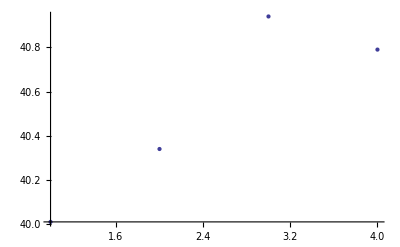

```mathematica
ListPlot[dataMicro]
```

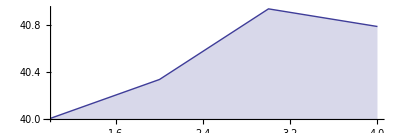

```mathematica
ListLinePlot[dataMicro, Filling->Bottom, AxesOrigin->{1,40}, AspectRatio->1/3]
```

```mathematica
Import["http://hispavila.com/3ds/elimages/fase1.gif"]
```

-Graphics-

```mathematica
pixels ={{44.,119.},{44.6667,127.},{46.6667,135.667},{49.3333,144.333},{52.6667,153.667},{56.,167.},{62.,183.},{70.,201.},{78.,215.},{88.,225.667},{82.,221.},{93.3333,225.667},{98.6667,222.333},{103.333,217.667},{106.,212.333},{109.333,207.667},{112.667,201.},{116.,193.667},{122.,179.667},{126.,165.},{132.667,149.},{124.667,171.},{118.,189.667},{134.667,138.333},{138.,125.},{144.,106.333},{148.667,93.},{151.333,79.6667},{154.,70.3333},{156.667,59.6667},{162.,44.3333},{168.667,35.6667},{170.667,28.3333},{178.667,16.3333},{184.667,12.3333},{193.333,9.},{174.667,21.6667},{200.667,15.6667},{204.667,23.},{210.,31.6667},{213.333,41.},{219.333,55.6667},{223.333,67.6667},{228.,78.3333},{230.667,91.},{234.,101.667},{236.,109.667},{237.333,115.667}}
```

{{44.,119.},{44.6667,127.},{46.6667,135.667},{49.3333,144.333},{52.6667,153.667},{56.,167.},{62.,183.},{70.,201.},{78.,215.},{88.,225.667},{82.,221.},{93.3333,225.667},{98.6667,222.333},{103.333,217.667},{106.,212.333},{109.333,207.667},{112.667,201.},{116.,193.667},{122.,179.667},{126.,165.},{132.667,149.},{124.667,171.},{118.,189.667},{134.667,138.333},{138.,125.},{144.,106.333},{148.667,93.},{151.333,79.6667},{154.,70.3333},{156.667,59.6667},{162.,44.3333},{168.667,35.6667},{170.667,28.3333},{178.667,16.3333},{184.667,12.3333},{193.333,9.},{174.667,21.6667},{200.667,15.6667},{204.667,23.},{210.,31.6667},{213.333,41.},{219.333,55.6667},{223.333,67.6667},{228.,78.3333},{230.667,91.},{234.,101.667},{236.,109.667},{237.333,115.667}}

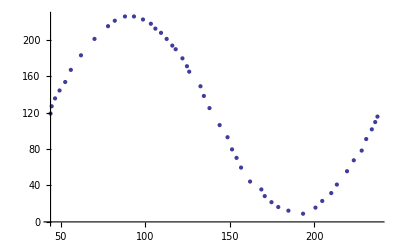

```mathematica
ListPlot[pixels]
```

Darth Vader Curve

WolframAlphaQueryResults

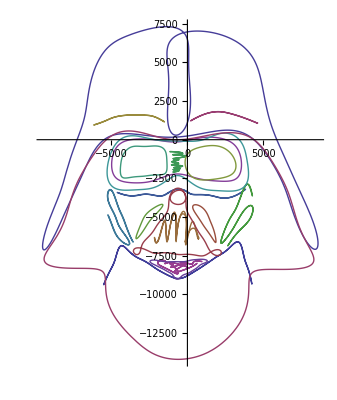

```mathematica
ParametricPlot[{{-492.571-8.28571 Sin[1.55556-16. t]-5.54545 Sin[1.55556-12. t]-5.375 Sin[1.5-10. t]-15.4286 Sin[1.57143-8. t]-21.4444 Sin[1.55556-6. t]-13.25 Sin[1.33333-5. t]+4685.25 Sin[1.57143+t]+71.2 Sin[4.7+2. t]+71.8 Sin[1.57143+3. t]+14.0213 Sin[4.71429+4. t]+33.8571 Sin[1.57143+7. t]+63.5714 Sin[1.6+9. t]+29.4 Sin[1.6+11. t]+6.5 Sin[1.5+13. t]+1.55556 Sin[1.28571+14. t]+0.75 Sin[0.6+15. t],-7974.63-59. Sin[1.55556-16. t]-2.5 Sin[1.33333-15. t]-66.5714 Sin[1.54545-14. t]-2.8 Sin[1.55556-13. t]-22.0833 Sin[1.57143-12. t]-92.5 Sin[1.57143-8. t]-12.6667 Sin[1.57143-7. t]-315.375 Sin[1.57143-6. t]-1013.43 Sin[1.57143-4. t]-90.2 Sin[1.55556-3. t]+116.2 Sin[1.57143+t]+117.833 Sin[1.6+2. t]+8.02778 Sin[1.33333+5. t]+13.2857 Sin[1.71429+9. t]+65.7778 Sin[1.625+10. t]+15.2222 Sin[4.66667+11. t]},{2407.29+2019.44 Sin[1.57143+t]+11.6667 Sin[1.55556+2. t]+199.167 Sin[1.57143+3. t]+9.04545 Sin[1.57143+4. t],1495.67-38.875 Sin[1.57143-4. t]-323.8 Sin[1.57143-2. t]-117.75 Sin[1.57143-1. t]+35.6667 Sin[1.57143+3. t]},{-3829.6-5.4 Sin[1.55556-8. t]-7.66667 Sin[1.54545-6. t]-7.8 Sin[1.55556-4. t]+2027.17 Sin[1.57143+t]+17.8 Sin[1.57143+2. t]+198.333 Sin[1.57143+3. t]+73.4 Sin[1.57143+5. t]+38.6667 Sin[1.57143+7. t],1394.93-23.8333 Sin[1.57143-6. t]-70.9 Sin[1.57143-4. t]-249.067 Sin[1.57143-2. t]+132.033 Sin[1.57143+t]+3.85714 Sin[4.71429+3. t]+24.1667 Sin[4.71429+5. t]+7.42857 Sin[4.71429+7. t]+6.16667 Sin[4.71429+8. t]},{-682.625-125.857 Sin[1.55556-16. t]-69.25 Sin[1.55556-12. t]-117. Sin[1.57143-11. t]-166. Sin[1.57143-10. t]-89.1429 Sin[1.57143-9. t]-142.6 Sin[1.57143-4. t]-70.6 Sin[1.57143-3. t]-2.6 Sin[1.57143-2. t]+49.75 Sin[1.57143+t]+3.6 Sin[4.625+5. t]+43.7 Sin[1.6+6. t]+12.9167 Sin[1.66667+7. t]+1.91667 Sin[2.16667+8. t]+15.125 Sin[4.66667+13. t]+84.4444 Sin[1.6+14. t]+18.75 Sin[1.55556+15. t]+113.857 Sin[1.6+17. t],-1405.67-2.2 Sin[1.55556-17. t]-8.05 Sin[1.55556-16. t]-7.42857 Sin[1.57143-12. t]-1.5 Sin[1.5-11. t]-6.7 Sin[1.55556-10. t]-2.16667 Sin[1.55556-4. t]+573. Sin[1.57143+t]+9.05263 Sin[4.71429+2. t]+30.8333 Sin[1.57143+3. t]+25.5714 Sin[1.57143+5. t]+4.11111 Sin[1.57143+6. t]+15.8 Sin[1.57143+7. t]+4.66667 Sin[1.57143+8. t]+15.2857 Sin[1.6+9. t]+1.75 Sin[1.6+13. t]+0.916667 Sin[4.57143+14. t]+2.7 Sin[1.6+15. t]},{-305.97-40.5 Sin[1.5-6. t]-13.0625 Sin[0.928571-4. t]-20.6 Sin[1.125-2. t]+3487.86 Sin[1.57143+t]+523.667 Sin[1.57143+3. t]+115.75 Sin[1.57143+5. t]+61.1429 Sin[1.57143+7. t]+19.1111 Sin[1.375+8. t]+31.6667 Sin[1.5+9. t]+40.5714 Sin[4.625+10. t],-3513.4+11.6667 Sin[4.71429+t]+61.1111 Sin[4.7+2. t]+63.75 Sin[1.54545+3. t]+163.167 Sin[1.55556+4. t]+27.2222 Sin[1.5+5. t]+25.25 Sin[1.54545+6. t]+74.5455 Sin[1.5+7. t]+62.4286 Sin[1.5+8. t]+48.4286 Sin[4.66667+9. t]+18.75 Sin[1.5+10. t]},{-610.25-57.3333 Sin[1.57143-13. t]-115.286 Sin[1.57143-9. t]+172.8 Sin[1.57143+t]+863.571 Sin[1.57143+2. t]+45.3333 Sin[1.55556+3. t]+4.16667 Sin[4.28571+4. t]+82.125 Sin[1.57143+5. t]+249.03 Sin[1.57143+6. t]+123.4 Sin[4.71429+7. t]+99.5 Sin[1.57143+8. t]+267.034 Sin[1.57143+10. t]+58.75 Sin[1.55556+11. t]+55.8333 Sin[4.71429+12. t]+136.6 Sin[4.71429+14. t]+42. Sin[1.57143+15. t]+35.625 Sin[1.57143+16. t]+9.03226 Sin[4.7+17. t]+106.75 Sin[1.57143+18. t]+56.4 Sin[1.57143+19. t]+6.4 Sin[4.66667+20. t]+17. Sin[1.57143+21. t],-8136.14-6.25 Sin[1.57143-19. t]-124.2 Sin[1.57143-5. t]+99.6 Sin[1.57143+t]+1.375 Sin[4.4+2. t]+173.933 Sin[1.57143+3. t]+49.6667 Sin[1.6+4. t]+10.4 Sin[4.66667+6. t]+27.1 Sin[1.55556+7. t]+158.857 Sin[1.57143+8. t]+92.8333 Sin[4.71429+9. t]+13.625 Sin[4.66667+10. t]+67.1667 Sin[4.71429+11. t]+37.6667 Sin[1.6+12. t]+76.125 Sin[1.57143+13. t]+1.375 Sin[4.5+14. t]+27.5714 Sin[1.57143+15. t]+11.7 Sin[1.57143+16. t]+40.8 Sin[4.71429+17. t]+7.7 Sin[4.71429+18. t]+20.05 Sin[4.71429+20. t]+18.6667 Sin[4.71429+21. t]},{-677.125-57.6667 Sin[1.53846-8. t]-26.6667 Sin[0.4-4. t]+1120.2 Sin[1.57143+t]+21.625 Sin[0.75+2. t]+229.714 Sin[1.46154+3. t]+74.4 Sin[1.28571+5. t]+22.1429 Sin[0.75+6. t]+90.25 Sin[1.5+7. t]+49.0357 Sin[4.66667+9. t]+24.4 Sin[4.375+10. t]+17.9 Sin[4.14286+11. t]+14.7 Sin[2.4+12. t]+13.25 Sin[2.16667+13. t]+16.6 Sin[1.7+14. t],-5840.2-65.5714 Sin[0.125-13. t]-91.8 Sin[1.4-11. t]+17.8 Sin[2.06667+t]+373.545 Sin[4.66667+2. t]+23. Sin[2.875+3. t]+117.043 Sin[4.44444+4. t]+74.4615 Sin[2.25+5. t]+200.167 Sin[1.83333+6. t]+203.4 Sin[1.8+7. t]+629.375 Sin[4.66667+8. t]+188.556 Sin[4.6+9. t]+142.286 Sin[1.625+10. t]+166. Sin[1.33333+12. t]+147.2 Sin[1.03704+14. t]},{3339.78-24.9 Sin[1.44444-6. t]-367.571 Sin[1.57143-4. t]-25.3333 Sin[1.55556-1. t]+517.25 Sin[1.57143+2. t]+675.444 Sin[1.57143+3. t]+116.556 Sin[1.57143+5. t]+57.0217 Sin[1.6+7. t]+19.5 Sin[1.5+8. t]+39.5 Sin[4.66667+9. t]+18.2 Sin[4.71429+10. t]+24.75 Sin[1.6+11. t],-5032.+951.375 Sin[1.57143+t]+699.333 Sin[1.57143+2. t]+909.8 Sin[1.57143+3. t]+673.8 Sin[4.71429+4. t]+96.8 Sin[4.66667+5. t]+13.8889 Sin[1.625+6. t]+80.4 Sin[4.6+7. t]+133.5 Sin[4.66667+8. t]+104.286 Sin[4.625+9. t]+120.941 Sin[4.66667+10. t]+35. Sin[1.71429+11. t]},{-4527.86-31.4706 Sin[1.55556-10. t]-223.714 Sin[1.57143-4. t]+179.375 Sin[1.6+t]+264.778 Sin[1.6+2. t]+572.2 Sin[1.6+3. t]+48.3333 Sin[1.57143+5. t]+42.4286 Sin[1.6+6. t]+5.2 Sin[4.16667+7. t]+79.1 Sin[1.625+8. t]+10.2 Sin[4.57143+9. t]+44.1667 Sin[1.6+11. t]+6.66667 Sin[4.5+12. t],-5224.87-56.0455 Sin[1.4-9. t]-113.2 Sin[1.45455-8. t]-61.0833 Sin[1.55556-7. t]-131.286 Sin[1.57143-5. t]-1185.67 Sin[1.55556-3. t]-734.75 Sin[1.55556-2. t]+558.909 Sin[1.57143+t]+169.286 Sin[1.5+4. t]+123.077 Sin[1.6+6. t]+11.8 Sin[1.28571+10. t]+7.88889 Sin[4.33333+11. t]+32.8 Sin[1.625+12. t]},{-713.429-21.5714 Sin[0.857143-7. t]+3977.5 Sin[1.66667+t]+51.375 Sin[0.111111+2. t]+305.067 Sin[1.83333+3. t]+21.4 Sin[3.4+4. t]+12.2222 Sin[2.03226+5. t]+6.11111 Sin[3.6+6. t],-1354.86-23.4 Sin[0.8-6. t]-36.25 Sin[1.25-4. t]-187.286 Sin[1.4-2. t]+1555.1 Sin[0.111111+t]+518. Sin[0.2+3. t]+39.9412 Sin[0.4+5. t]+43.1667 Sin[0.833333+7. t]},{1216.8+695.2 Sin[1.33333+t]+86.6 Sin[4.16667+2. t]+82.7143 Sin[1.66667+3. t]+22.6 Sin[4.6+4. t],-5378.17-18.5714 Sin[1.125-4. t]-106.75 Sin[0.96-3. t]-1110.67 Sin[1.28571-1. t]+49.0526 Sin[4.28571+2. t]},{-2584.89-88.4286 Sin[1.28571-3. t]+802. Sin[4.625+t]+84.2 Sin[1.57143+2. t],-5208.56-86.0769 Sin[1.11111-3. t]-81.5294 Sin[1.33333-2. t]-1025.75 Sin[1.28571-1. t]},{-605.-17.75 Sin[0.777778-9. t]-32.1111 Sin[0.857143-8. t]-307.333 Sin[0.1-3. t]-100.028 Sin[1.25-2. t]+4386.14 Sin[1.+t]+78.4444 Sin[0.833333+4. t]+18.9286 Sin[2.2+5. t]+30.8889 Sin[0.125+6. t]+34.1 Sin[0.8+7. t],-1538.09-1871.25 Sin[0.555556-1. t]+212.111 Sin[3.77778+2. t]+715.25 Sin[4.6+3. t]+5.5 Sin[3.5+4. t]+13.875 Sin[1.71429+5. t]+63.875 Sin[1.06667+6. t]+25.7143 Sin[2.75+7. t]+69.75 Sin[3.4+8. t]+15.2 Sin[4.05+9. t]},{-610.167+1537.71 Sin[4.44444+t]+129.75 Sin[2.54545+2. t]+176.75 Sin[3.85714+3. t]+48.9286 Sin[2.1+4. t]+50.7143 Sin[3.66667+5. t]+42.6667 Sin[1.4+6. t]+19.2 Sin[3.22222+7. t]+30.2222 Sin[1.05882+8. t]+8.875 Sin[3.2+9. t]+18.1429 Sin[0.571429+10. t]+7.88889 Sin[4.28571+11. t]+15.3333 Sin[0.285714+12. t],-8158.62-5.46154 Sin[0.5-11. t]-19.8333 Sin[1.0625-6. t]-41.7143 Sin[1.42857-5. t]-4.92308 Sin[0.6-3. t]-497.667 Sin[0.285714-1. t]+235.375 Sin[1.16667+2. t]+24.4286 Sin[3.55556+4. t]+10.04 Sin[1.+7. t]+17.5 Sin[2.28571+8. t]+11.7 Sin[3.75+9. t]+4.77778 Sin[3.625+10. t]+4.77778 Sin[1.53846+12. t]},{-684.375-16.4286 Sin[0.142857-13. t]-35.5385 Sin[0.166667-9. t]-117.667 Sin[1.2-7. t]-1077.17 Sin[0.833333-2. t]+113.333 Sin[8. t]+1907.08 Sin[1.2+t]+63.2857 Sin[3.8+3. t]+21.0714 Sin[2.5+4. t]+209.429 Sin[2.7+5. t]+57.6 Sin[3.25+6. t]+33.125 Sin[2.28571+10. t]+8.57143 Sin[4.2+11. t]+48.9474 Sin[2.28571+12. t],-5784.5-34.8 Sin[0.571429-8. t]-197.043 Sin[0.833333-6. t]+2117.94 Sin[2.77778+t]+432.8 Sin[3.88889+2. t]+275.2 Sin[1.85714+3. t]+232.8 Sin[3.11111+4. t]+92.3333 Sin[3.8+5. t]+134.75 Sin[0.3+7. t]+69.9167 Sin[2.88889+9. t]+4.6 Sin[2.66667+10. t]+40.9545 Sin[2.2+11. t]+32.6 Sin[0.555556+12. t]+19.2857 Sin[4.5+13. t]},{1452.29+1649.5 Sin[1.16667+t]+75.4 Sin[1.16667+2. t]+23.1667 Sin[0.285714+3. t],-1515.2-1160.2 Sin[0.454545-1. t]+24.4286 Sin[4.2+2. t]+86.8889 Sin[4.25+3. t]},{-2885.14-1590.95 Sin[1.06667-1. t]+28.5714 Sin[2.91667+2. t]+35.1111 Sin[2.33333+3. t]+35.6 Sin[1.71429+4. t]+40.5556 Sin[4.2+5. t]+2.57143 Sin[1.22222+6. t],-1488.2-11.3333 Sin[1.-4. t]-119.714 Sin[0.5-2. t]+1112.57 Sin[0.4+t]+150.714 Sin[1.57143+3. t]+21.9 Sin[3.8+5. t]+27.7143 Sin[4.45455+6. t]},{-606.625-64.25 Sin[0.958333-15. t]-517.75 Sin[0.333333-3. t]-2772.03 Sin[1.11111-2. t]+7327.14 Sin[1.+t]+673.778 Sin[0.75+4. t]+499.4 Sin[1.77778+5. t]+301.625 Sin[2.75+6. t]+265.952 Sin[1.+7. t]+164.333 Sin[1.66667+8. t]+78.0909 Sin[1.5+9. t]+92.4 Sin[3.71429+10. t]+105.25 Sin[2.+11. t]+91.875 Sin[2.5+12. t]+63. Sin[2.66667+13. t]+60.7143 Sin[3.94444+14. t],394.2-104.5 Sin[0.833333-8. t]+4148.93 Sin[2.625+t]+1937.67 Sin[3.71429+2. t]+3672.71 Sin[1.42857+3. t]+853.875 Sin[2.25+4. t]+369.3 Sin[2.92308+5. t]+921.857 Sin[4.28571+6. t]+181.455 Sin[3.2+7. t]+160.955 Sin[1.25+9. t]+78.0345 Sin[1.94444+10. t]+93.0217 Sin[0.2+11. t]+130.75 Sin[4.2+12. t]+46.5714 Sin[2.625+13. t]+56.5714 Sin[4.2+14. t]+85.0588 Sin[0.666667+15. t]},{-559.375-575.286 Sin[1.33333-5. t]+7908.71 Sin[1.+t]+774.667 Sin[1.9375+2. t]+100.714 Sin[1.22222+3. t]+199.455 Sin[1.04+4. t]+108.556 Sin[3.25+6. t]+284. Sin[3.85714+7. t]+146.571 Sin[1.4+8. t]+84.625 Sin[2.71429+9. t]+127.875 Sin[0.555556+10. t],-6496.67-187.6 Sin[0.888889-7. t]+6675.25 Sin[2.57143+t]+270.03 Sin[3.5+2. t]+769.167 Sin[4.57143+3. t]+787.043 Sin[2.4+4. t]+161.286 Sin[3.25+5. t]+67.5714 Sin[1.42857+6. t]+95.8571 Sin[0.0714286+8. t]+1.75 Sin[4.5+9. t]+54.5556 Sin[2.07143+10. t]}},{t,0,2 π}]
```